1/2

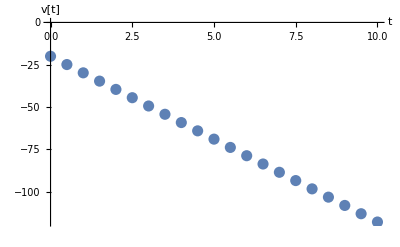

The numerical value of the final velocity at 10 seconds is -118

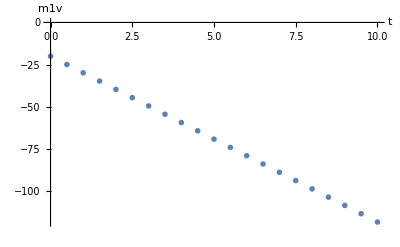

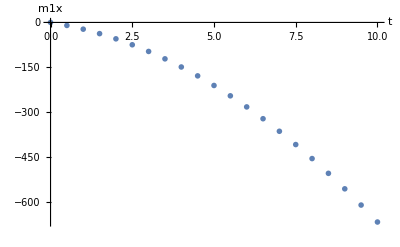

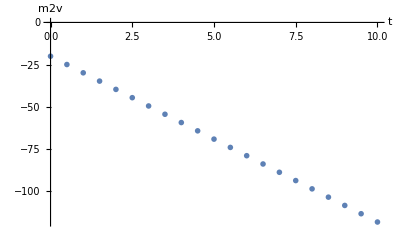

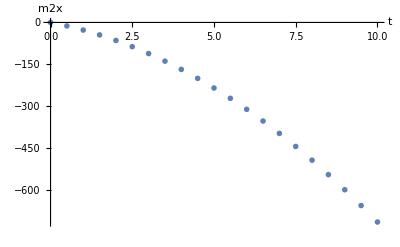

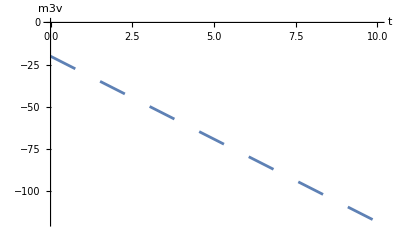

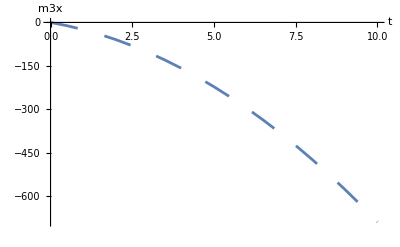

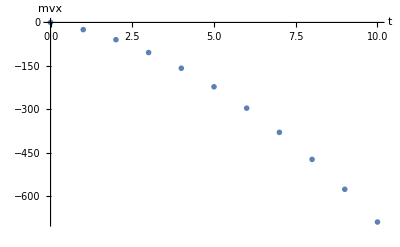

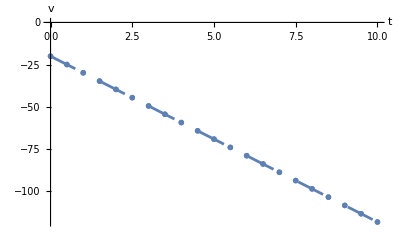

Part::partd: Part specification {{0.,0.},{1.,-24.905},{2.,-59.62},{3.,-104.145},{4.,-158.48},{5.,-222.625},{6.,-296.58},{7.,-380.345},{8.,-473.92},{9.,-577.305},«1»}⟦0.,2⟧ is longer than depth of object.

Clear::ssym: v[ti] is not a symbol or a valid string pattern.

1/2

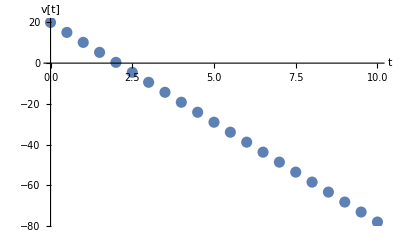

{{0.,0},{0.5,10},{1.,17.5475},{1.5,22.6425},{2.,25.285},{2.5,25.475},{3.,23.2125},{3.5,18.4975},{4.,11.33},{4.5,1.71},{5.,-10.3625},{5.5,-24.8875},{6.,-41.865},{6.5,-61.295},{7.,-83.1775},{7.5,-107.513},{8.,-134.3},{8.5,-163.54},{9.,-195.233},{9.5,-229.378},{10.,-265.975}}

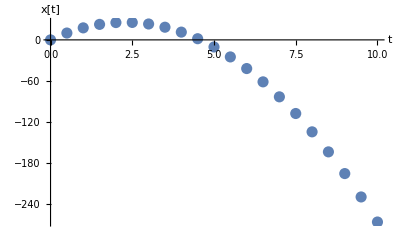

The numerical value of the final velocity at 10 seconds is -78

{{0,v[0]},{1/2,v[1/2]},{1,v[1]},{3/2,v[3/2]},{2,v[2]},{5/2,v[5/2]},{3,v[3]},{7/2,v[7/2]},{4,v[4]},{9/2,v[9/2]},{5,v[5]},{11/2,v[11/2]},{6,v[6]},{13/2,v[13/2]},{7,v[7]},{15/2,v[15/2]},{8,v[8]},{17/2,v[17/2]},{9,v[9]},{19/2,v[19/2]},{10,v[10]}}

{{0,x[0]},{1/2,x[1/2]},{1,x[1]},{3/2,x[3/2]},{2,x[2]},{5/2,x[5/2]},{3,x[3]},{7/2,x[7/2]},{4,x[4]},{9/2,x[9/2]},{5,x[5]},{11/2,x[11/2]},{6,x[6]},{13/2,x[13/2]},{7,x[7]},{15/2,x[15/2]},{8,x[8]},{17/2,x[17/2]},{9,x[9]},{19/2,x[19/2]},{10,x[10]}}

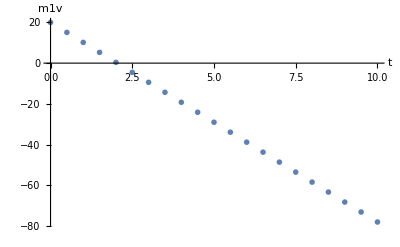

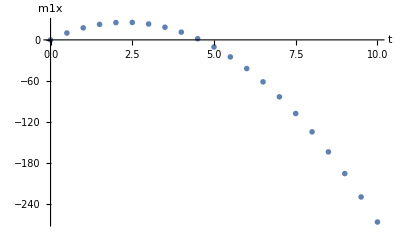

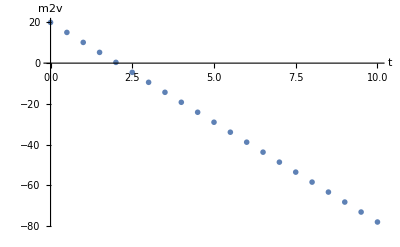

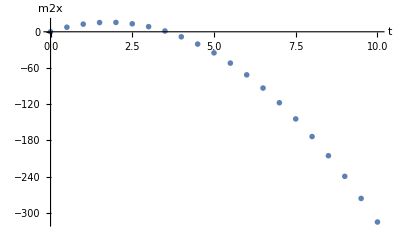

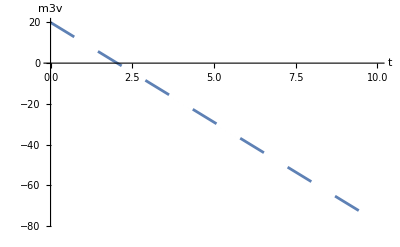

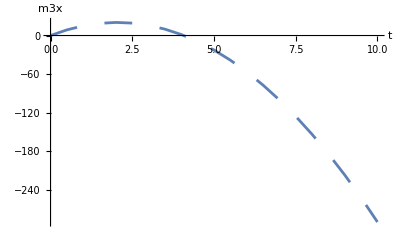

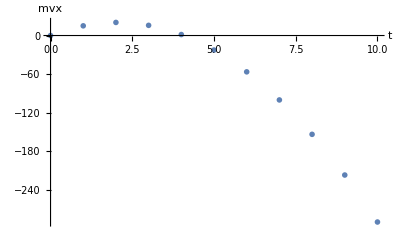

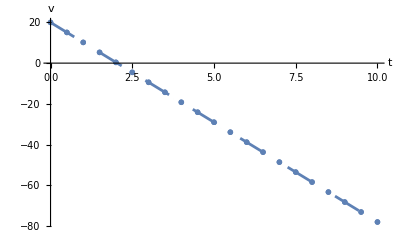

Part::partd: Part specification {{0.,0.},{1.,15.095},{2.,20.38},{3.,15.855},{4.,1.52},{5.,-22.625},{6.,-56.58},{7.,-100.345},{8.,-153.92},{9.,-217.305},«1»}⟦0.,2⟧ is longer than depth of object.

```mathematica
Clear[x,v];
x[ti]=0;v[ti]=-20;a=-9.8;Δt=5/10
Do[v[t+Δt]=v[t]+a*Δt;
x[t+Δt]=x[t]+v[t]*Δt,{t,ti,tf,Δt}]

Vdata:=Table[{t,v[t]},{t,ti,tf,Δt}];
ListPlot[Vdata,AxesLabel->{"t","v[t]"},PlotStyle->PointSize[0.02]]

Ydata:=Table[{t,x[t]},{t,ti,tf,Δt}]
Plot1:=ListPlot[Ydata,AxesLabel->{"t","x[t]"},PlotStyle->PointSize[0.02]]

SetOptions[Graphics,AspectRatio->Automatic,Axes->Automatic,AxesLabel->{"x","y"},PlotRange->{{-1,300},{-500,10}}];

Print["The numerical value of the final velocity at 10 seconds is -118"]


(*Forward Euler Method*)
Clear[v,t];v[0.]=-20.;Δt=5/10;a=-9.81;
Do[v[t+Δt]=v[t]+a*Δt;
x[t+Δt]=x[t]+v[t]*Δt,{t,ti,tf,Δt}]
data1:=Table[{t,v[t]},{t,0,10,Δt}]
data2:=Table[{t,x[t]},{t,0,10,Δt}]
NumGraph1=ListPlot[data1,AxesOrigin->{0,0},AxesLabel->{t,m1v},PlotStyle->PointSize[0.01]]
NumGraph2=ListPlot[data2,AxesOrigin->{0,0},AxesLabel->{t,m1x},PlotStyle->PointSize[0.01]]

(*Euler-Cromer Method*)
Clear[v,t];
ti=0.;tf=10.;Δt=5/10;
x[ti]=0;v[ti]=-20.;a=-9.81;
Do[v[t+Δt]=v[t]+a*Δt;
x[t+Δt]=x[t]+v[t+Δt]*Δt,{t,ti,tf,Δt}]

data3:=Table[{t,v[t]},{t,ti,tf,Δt}];
data4:=Table[{t,x[t]},{t,ti,tf,Δt}];
NumGraph3=ListPlot[data3,AxesOrigin->{0,0},AxesLabel->{t,m2v},PlotStyle->PointSize[0.01]]
NumGraph4=ListPlot[data4,AxesOrigin->{0,0},AxesLabel->{t,m2x},PlotStyle->PointSize[0.01]]

(*Euler-Trapezoidal Method*)
Clear[v,t];
ti=0.;tf=10.;Δt=5/10;
x[ti]=0;v[ti]=-20.;a=-9.81;
Do[v[t+Δt]=v[t]+a*Δt;
x[t+Δt]=x[t]+.5*(v[t+Δt]+v[t])*Δt,{t,ti,tf,Δt}]

data5:=Table[{t,v[t]},{t,ti,tf,Δt}];
data6:=Table[{t,x[t]},{t,ti,tf,Δt}];
NumGraph5=ListPlot[data5,AxesOrigin->{0,0},AxesLabel->{t,m3v},Joined->True,PlotStyle->Dashing[{0.05}]]
NumGraph6=ListPlot[data6,AxesOrigin->{0,0},AxesLabel->{t,m3x},Joined->True,PlotStyle->Dashing[{0.05}]]

(*Verlet Method*)
Verlet[a_,x0_,v0_,dt_,ns_]:=Module[{xout,xnext,xcur,xprev,t,index},
xout=Table[0.0,{j,1,ns}];
xcur=x0;
xprev=x0-dt*v0+(1/2) a[x0,0.0] dt^2;
t=0.0;
xout⟦1⟧={t,x0};
For[index=2,index≤ns,index=index+1,xnext=2.0 xcur-xprev+dt^2 a[xcur,t];
t=t+dt;
xout⟦index⟧={t,xnext};
xprev=xcur;
xcur=xnext;];
Return[xout];]

Clear[Pdata];

Clear[y];
Δt=1;
a1[x_,t_]:=-9.81;

Nsteps=11;
data7:=Verlet[a1,0.0,-20.0,Δt,Nsteps];

NumGraph7=ListPlot[data7,AxesOrigin->{0,0},AxesLabel->{t,mvx},PlotStyle->PointSize[0.01]]


Show[NumGraph1,NumGraph3,NumGraph5,AxesLabel->{t,v}]
Show[NumGraph2,NumGraph4,NumGraph6,NumGraph7,AxesLabel->{t,x}]

SetOptions[Graphics,AspectRatio->Automatic,Axes->Automatic,AxesLabel->{"x","y"},PlotRange->{{-1,300},{-500,10}}];

P1data=Table[data7[[t,2]],{t,ti,tf,Δt}];

Animate[Graphics[{Point[{150,P1data[[n]]}],PointSize[0.10]}],{n,ti,tf,Δt},AnimationRunning->False]




Clear[Pdata,data1,data2,data3,data4,data5,data6,data7,v[ti],a];

Clear[x,v];
x[ti]=0;v[ti]=20;a=-9.81;Δt=5/10
Do[v[t+Δt]=v[t]+a*Δt;
x[t+Δt]=x[t]+v[t]*Δt,{t,ti,tf,Δt}]

Vdata=Table[{t,v[t]},{t,ti,tf,Δt}];
ListPlot[Vdata,AxesLabel->{"t","v[t]"},PlotStyle->PointSize[0.02]]

Xdata=Table[{t,x[t]},{t,ti,tf,Δt}]
Plot1=ListPlot[Xdata,AxesLabel->{"t","x[t]"},PlotStyle->PointSize[0.02]]

SetOptions[Graphics,AspectRatio->Automatic,Axes->Automatic,AxesLabel->{"x","y"},PlotRange->{{-1,300},{-500,10}}];

Print["The numerical value of the final velocity at 10 seconds is -78"]


(*Forward Euler Method*)
Clear[v,t];v[0.]=20.;Δt=5/10;a=-9.81;
Do[v[t+Δt]=v[t]+a*Δt;
x[t+Δt]=x[t]+v[t]*Δt,{t,ti,tf,Δt}]
data1=Table[{t,v[t]},{t,0,10,Δt}]
data2=Table[{t,x[t]},{t,0,10,Δt}]
NumGraph1=ListPlot[data1,AxesOrigin->{0,0},AxesLabel->{t,m1v},PlotStyle->PointSize[0.01]]
NumGraph2=ListPlot[data2,AxesOrigin->{0,0},AxesLabel->{t,m1x},PlotStyle->PointSize[0.01]]

(*Euler-Cromer Method*)
Clear[v,t];
ti=0.;tf=10.;Δt=5/10;
x[ti]=0;v[ti]=20.;a=-9.81;
Do[v[t+Δt]=v[t]+a*Δt;
x[t+Δt]=x[t]+v[t+Δt]*Δt,{t,ti,tf,Δt}]

data3=Table[{t,v[t]},{t,ti,tf,Δt}];
data4=Table[{t,x[t]},{t,ti,tf,Δt}];
NumGraph3=ListPlot[data3,AxesOrigin->{0,0},AxesLabel->{t,m2v},PlotStyle->PointSize[0.01]]
NumGraph4=ListPlot[data4,AxesOrigin->{0,0},AxesLabel->{t,m2x},PlotStyle->PointSize[0.01]]

(*Euler-Trapezoidal Method*)
Clear[v,t];
ti=0.;tf=10.;Δt=5/10;
x[ti]=0;v[ti]=20.;a=-9.81;
Do[v[t+Δt]=v[t]+a*Δt;
x[t+Δt]=x[t]+.5*(v[t+Δt]+v[t])*Δt,{t,ti,tf,Δt}]

data5=Table[{t,v[t]},{t,ti,tf,Δt}];
data6=Table[{t,x[t]},{t,ti,tf,Δt}];
NumGraph5=ListPlot[data5,AxesOrigin->{0,0},AxesLabel->{t,m3v},Joined->True,PlotStyle->Dashing[{0.05}]]
NumGraph6=ListPlot[data6,AxesOrigin->{0,0},AxesLabel->{t,m3x},Joined->True,PlotStyle->Dashing[{0.05}]]

(*Verlet Method*)
Verlet[a_,x0_,v0_,dt_,ns_]:=Module[{xout,xnext,xcur,xprev,t,index},
xout=Table[0.0,{j,1,ns}];
xcur=x0;
xprev=x0-dt*v0+(1/2) a[x0,0.0] dt^2;
t=0.0;
xout⟦1⟧={t,x0};
For[index=2,index≤ns,index=index+1,xnext=2.0 xcur-xprev+dt^2 a[xcur,t];
t=t+dt;
xout⟦index⟧={t,xnext};
xprev=xcur;
xcur=xnext;];
Return[xout];]

Clear[y];
Δt=1;
a1[x_,t_]:=-9.81;

Nsteps=11;
data7=Verlet[a1,0.0,20.0,Δt,Nsteps];

NumGraph7=ListPlot[data7,AxesOrigin->{0,0},AxesLabel->{t,mvx},PlotStyle->PointSize[0.01]]


Show[NumGraph1,NumGraph3,NumGraph5,AxesLabel->{t,v}]
Show[NumGraph2,NumGraph4,NumGraph6,NumGraph7,AxesLabel->{t,x}]

SetOptions[Graphics,AspectRatio->Automatic,Axes->Automatic,AxesLabel->{"x","y"},PlotRange->{{-1,300},{-500,10}}];

P2data=Table[data7[[t,2]],{t,ti,tf,Δt}];

Animate[Graphics[{Point[{150,P2data[[n]]}],PointSize[0.10]}],{n,ti,tf,Δt},AnimationRunning->False]
```